# Solar wind discontinuities and ion scattering

```mathematica
$Path=Join[$Path,{NotebookDirectory[]}];
<<utilities.wl
<<m/rules.wl
```

```mathematica
(*(*SetOptions[$FrontEndSession,GraphicsBoxOptions->{AxesStyle->Large}]*)
(*SetOptions[ParametricPlot3D,AxesStyle->Large];*)
(*SetOptions[$FrontEndSession,GraphicsBoxOptions->{AxesStyle->{}}]*)*)
```

```mathematica
On[Assert];
notationRules=Join[
{B0->Subscript[B, 0],α->θ,Bz->Subscript[B, z],B0in->Subscript[B, t]},
{f1->Subscript[f, 1][z],f2->Subscript[f, 2][z],Cβ->Subscript[C, β]},
{xN->x̃,zN->z̃},
{pxN->OverTilde[Subscript[p, x]],pzN->OverTilde[Subscript[p, z]]},
{px->Subscript[p, x],py->Subscript[p, y],pz->Subscript[p, z]}
];
formRules=notationRules;
assums={c>0,q>0,L>0,B0>0,B0in>0};
```

## Introduction

## Theoretical Analysis

Notation α=ρ/L

## Deduction

```mathematica
BRules={
Bx[z_]:> B0in Sin[β Tanh[z/L]],
By[z_]:> B0in Cos[β Tanh[z/L]],
B0in->B0 Sin[α],Bz->B0 Cos[α]
};
B2Rules={Bx[z_]:> B0in Tanh[z/L],By[z_]:> CBy};
B3Rules={Bx[z_]:> B0in z/L,By[z_]:> B0in √(1-(z/L)^2)};
B3AntonRules={Bx[z_]:> B0in z/L,By[z_]:> B0in(1-z^2/(2 L^2))};
```

```mathematica
Ax:=Integrate[By[z],z]
Ay:=Integrate[-Bx[z],z]+ Integrate[Bz,x]
Az:=0
```

```mathematica
vecA:= {Ax,Ay,Az}
vecP={px,py,pz};
vecV:=vecP-(q vecA)/c;
Assert[(vecA{x,y,z})=={Bx[z],By[z],Bz}]
```

```mathematica
RHS:=1/(2m)vecV.vecV + q V/.{V->0}
rawEq:=rawH ==RHS
rawEq
```

rawH==(pz^2+(py-(q (Bz x-∫Bx[z]ⅆz))/c)^2+(px-(q ∫By[z]ⅆz)/c)^2)/(2 m)

```mathematica
fRules={f1->Integrate[By[z],z]/(B0in  L) ,f2->Integrate[-Bx[z],z]/(B0in  L) };
Ax:= f1 B0in L
Ay:= f2 B0in L  + Integrate[Bz,x]
```

#### Notations

```mathematica
{Subscript[A, x]->Ax,Subscript[A, y]->Ay}//.notationRules
Collect[{Subscript[f, 1]->f1,Subscript[f, 2]->f2}//.Join[fRules,BRules],{Cos[β],Sin[β]} ]
```

{A_x→L B_t f_1[z],A_y→x B_z+L B_t f_2[z]}

{f_1→1/2 Cos[β] (-CosIntegral[β-β Tanh[z/L]]+CosIntegral[β+β Tanh[z/L]])+1/2 Sin[β] (-SinIntegral[β-β Tanh[z/L]]+SinIntegral[β+β Tanh[z/L]]),f_2→1/2 (CosIntegral[β-β Tanh[z/L]]+CosIntegral[β+β Tanh[z/L]]) Sin[β]+1/2 Cos[β] (-SinIntegral[β-β Tanh[z/L]]-SinIntegral[β+β Tanh[z/L]])}

```mathematica
applyRules[x_,BRules_]:=x//.Join[fRules,BRules]//.normRules
```

## Normalization

Normalize p=p̃ p, r =r̃ l with l=L
So H=H̃ h

```mathematica
normRules:=Join[
(*{Bref->B0,Lref->L,B0in->B0inN Bref},*)
{Bref->B0in},
{Lref->L,x->Lref xN + cxN1 ,cxN1->(c py)/(q Bz),z->zN Lref},
{Bref->B0in,p->(Bref q Lref)/c,px->pxN p,py->pyN p,pz->pzN p,m->(Bref^2 q^2 Lref^2)/(c^2 h)}];
```

```mathematica
HBar:=1/2  ( pzN^2+(pxN-f1 B0in/Bref)^2+(xN Bz/Bref+f2 B0in/Bref)^2)
Assert[Simplify[( h HBar-RHS)//.normRules]==0,assums]
```

```mathematica
"H̃"->HBar//.Join[BRules,normRules]/.notationRules
```

H̃→1/2 (OverTilde[p_z]^2+(OverTilde[p_x]-f_1[z])^2+(Cot[θ] x̃+f_2[z])^2)

### Asymptotic Hamiltonian near z=0

```mathematica
fasym[f_,N_,BRules_]:={ff=Simplify[applyRules[f,BRules]]; f->Simplify[Series[ff,{zN,0,N}],assums],ff}
fasymB[BRules_,N_:3]:=Join[{BRules},{fasym[f1,#,BRules],fasym[f2,#,BRules]}/.notationRules& @N]
fasymB[BRules]
fasymB[B2Rules]
fasymB[B3Rules]
fasymB[B3AntonRules]
```

{{Bx[z_]:>B0in Sin[β Tanh[z/L]],By[z_]:>B0in Cos[β Tanh[z/L]],B0in→B0 Sin[α],Bz→B0 Cos[α]},{f_1[z]→z̃-1/6 β^2 (z̃)^3+O[z̃]^4,1/2 (-Cos[β] CosIntegral[β-β Tanh[z̃]]+Cos[β] CosIntegral[β+β Tanh[z̃]]+Sin[β] (-SinIntegral[β-β Tanh[z̃]]+SinIntegral[β+β Tanh[z̃]]))},{f_2[z]→(CosIntegral[β] Sin[β]-Cos[β] SinIntegral[β])-(β (z̃)^2)/2+O[z̃]^4,1/2 (CosIntegral[β-β Tanh[z̃]] Sin[β]+CosIntegral[β+β Tanh[z̃]] Sin[β]-Cos[β] (SinIntegral[β-β Tanh[z̃]]+SinIntegral[β+β Tanh[z̃]]))}}

{{Bx[z_]:>B0in Tanh[z/L],By[z_]:>CBy},{f_1[z]→(CBy z̃)/B_t+O[z̃]^4,(CBy z̃)/B_t},{f_2[z]→-(z̃)^2/2+O[z̃]^4,-Log[Cosh[z̃]]}}

{{Bx[z_]:>(B0in z)/L,By[z_]:>B0in √(1-(z/L)^2)},{f_1[z]→-1/2 π √(1/(z̃)^2) z̃+z̃-(z̃)^3/6+O[z̃]^4,ArcTan[(z̃)/(-1+√(1-(z̃)^2))]+1/2 z̃ √(1-(z̃)^2)},{f_2[z]→-(z̃)^2/2+O[z̃]^4,-(z̃)^2/2}}

{{Bx[z_]:>(B0in z)/L,By[z_]:>B0in (1-z^2/(2 L^2))},{f_1[z]→z̃-(z̃)^3/6+O[z̃]^4,z̃-(z̃)^3/6},{f_2[z]→-(z̃)^2/2+O[z̃]^4,-(z̃)^2/2}}

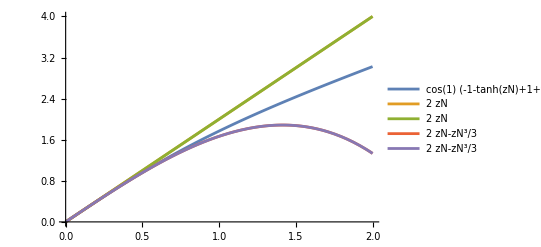

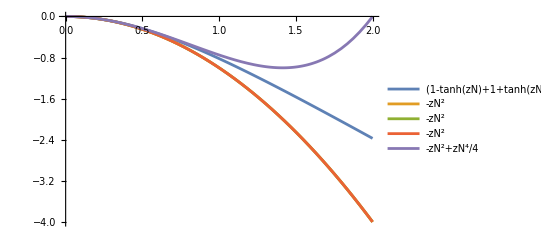

```mathematica
asyPlot[f_,n_:4,βTemp_:1]:=Block[{β=βTemp},
asyfs=Table[Asymptotic[f,{zN,0,i}],{i,n}];
Plot[{f,asyfs}//Evaluate,{zN,0,2},PlotLegends->"Expressions"]
]

asyPlot[f1/.fRules/.normRules]
asyPlot[f2/.fRules/.normRules]
```

## Equations

```mathematica
H:=HBar/.fRules/.normRules/.unNormRules
Ht:=H/.tRules
(*H:=1/2 pz[t]^2+1/2(px[t]-1/2 Sin[α]f1t)^2+1/2(Cos[α]x[t]+1/2 Sin[α]f2t)^2;*)
```

```mathematica
Ht
```

1/2 (pz[t]^2+(px[t]-1/2 Sin[α] (Cos[β] (-CosIntegral[β-β Tanh[z[t]]]+CosIntegral[β+β Tanh[z[t]]])+Sin[β] (-SinIntegral[β-β Tanh[z[t]]]+SinIntegral[β+β Tanh[z[t]]])))^2+(1/2 Sin[α] ((CosIntegral[β-β Tanh[z[t]]]+CosIntegral[β+β Tanh[z[t]]]) Sin[β]-2 (CosIntegral[β] Sin[β]-Cos[β] SinIntegral[β])-Cos[β] (SinIntegral[β-β Tanh[z[t]]]+SinIntegral[β+β Tanh[z[t]]]))+Cos[α] x[t])^2)

```mathematica
hamiltonianEquations:={
px'[t]==-D[Ht, x[t]],
x'[t]==D[Ht, px[t]],
pz'[t]==-D[Ht, z[t]],
z'[t]==D[Ht, pz[t]]
}
```

```mathematica
U:=Simplify[H-1/2 pz^2];
```

```mathematica
eq:={D[U,z]==0,D[U,z]<0,H==1/2/.{pz->0}}
sol:=NSolveValues[
eq,{x,px},Reals
]
```

```mathematica
tempPlot:=Block[{α=π/2-0.01,β=π/2},
sol=NSolveValues[
(D[U, z]==0)&&
(H==1/2)/.{pz->0},{x,px}];
ParametricPlot[sol,{z,-3,3},
PlotLabel->StringForm["c_1: `` c_2: ``",N@c1,N@c2]]
]
```